```mathematica
R[b_, t_]=FullSimplify[Integrate[64/Pi^2 Cos[s t]Exp[-b s] s^2 Exp[- 4 s^2/Pi], {s, 0, Infinity}]]
```

1/8 ⅇ^(-1/16 π t (2 ⅈ b+t)) (-8 b ⅇ^(1/16 π t (2 ⅈ b+t))+ⅇ^((b^2 π)/16) (8+π (b-ⅈ t)^2)-ⅇ^((b^2 π)/16) (8+π (b-ⅈ t)^2) Erf[1/4 √π (b-ⅈ t)]+ⅇ^(1/16 b π (b+4 ⅈ t)) (8+π (b+ⅈ t)^2) Erfc[1/4 √π (b+ⅈ t)])

```mathematica
G[b_, t_]=FullSimplify[Integrate[32/Pi^2 Exp[I s t]Exp[-b s] s^2 Exp[- 4 s^2/Pi], {s, 0, Infinity}]]
```

1/8 (-4 b+4 ⅈ t+ⅇ^(1/16 π (b-ⅈ t)^2) (8+π (b-ⅈ t)^2) Erfc[1/4 √π (b-ⅈ t)])

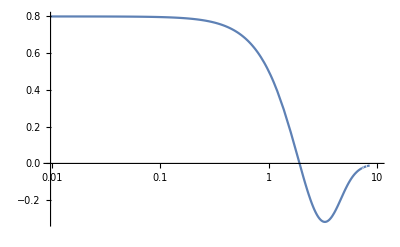

```mathematica
LogLinearPlot[R[1,t], {t, 0, 10}]
```

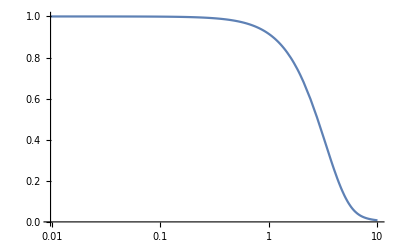

```mathematica
LogLinearPlot[Abs[G[0,t]], {t, 0, 10}]
```